# Symmetric Stable Cubics

We are interested in symmetric stable cubic polynomials. Any symmetric cubic can be written in the form

```mathematica
p=a*e3 + b*e2*e1+c*e1^3
```

c e1^3+b e1 e2+a e3

Here, ei denotes the degree i elementary symmetric mean, defined as the average of all of the k-wise products of the coordinates of the variables. 
There is a nice expression that you get when you consider ei(x+t1), which is

```mathematica
univariateRules={e1->e1+t, e2->e2+2 * e1*t + t^2, e3-> e3+ 3*e2*t+3*e1*t^2+t^3}
```

{e1→e1+t,e2→e2+2 e1 t+t^2,e3→e3+3 e2 t+3 e1 t^2+t^3}

Evaluating p with these rules gives

```mathematica
pUni=Collect[ReplaceAll[p,univariateRules],t]
```

c e1^3+b e1 e2+a e3+(2 b e1^2+3 c e1^2+3 a e2+b e2) t+(3 a e1+3 b e1+3 c e1) t^2+(a+b+c) t^3

To check that this is real rooted, we would want to take the discriminant

```mathematica
discr=Discriminant[pUni,t]
```

36 a^2 b^2 e1^6+40 a b^3 e1^6+4 b^4 e1^6-108 a^3 c e1^6-108 a^2 b c e1^6+36 a b^2 c e1^6+4 b^3 c e1^6-108 a^2 c^2 e1^6-108 a^2 b^2 e1^4 e2-120 a b^3 e1^4 e2-12 b^4 e1^4 e2+324 a^3 c e1^4 e2+324 a^2 b c e1^4 e2-108 a b^2 c e1^4 e2-12 b^3 c e1^4 e2+324 a^2 c^2 e1^4 e2+81 a^4 e1^2 e2^2+162 a^3 b e1^2 e2^2+189 a^2 b^2 e1^2 e2^2+120 a b^3 e1^2 e2^2+12 b^4 e1^2 e2^2-162 a^3 c e1^2 e2^2-162 a^2 b c e1^2 e2^2+108 a b^2 c e1^2 e2^2+12 b^3 c e1^2 e2^2-243 a^2 c^2 e1^2 e2^2-108 a^4 e2^3-216 a^3 b e2^3-144 a^2 b^2 e2^3-40 a b^3 e2^3-4 b^4 e2^3-108 a^3 c e2^3-108 a^2 b c e2^3-36 a b^2 c e2^3-4 b^3 c e2^3-108 a^4 e1^3 e3-216 a^3 b e1^3 e3-108 a^2 b^2 e1^3 e3-216 a^3 c e1^3 e3-216 a^2 b c e1^3 e3-108 a^2 c^2 e1^3 e3+162 a^4 e1 e2 e3+324 a^3 b e1 e2 e3+162 a^2 b^2 e1 e2 e3+324 a^3 c e1 e2 e3+324 a^2 b c e1 e2 e3+162 a^2 c^2 e1 e2 e3-27 a^4 e3^2-54 a^3 b e3^2-27 a^2 b^2 e3^2-54 a^3 c e3^2-54 a^2 b c e3^2-27 a^2 c^2 e3^2

To simplify notation, let us assume e1 = 1, and rename x = e2 and y = e3

```mathematica
discr = Discriminant[pUni,t]/.{e1->1, e2->x, e3->y}
```

36 a^2 b^2+40 a b^3+4 b^4-108 a^3 c-108 a^2 b c+36 a b^2 c+4 b^3 c-108 a^2 c^2-108 a^2 b^2 x-120 a b^3 x-12 b^4 x+324 a^3 c x+324 a^2 b c x-108 a b^2 c x-12 b^3 c x+324 a^2 c^2 x+81 a^4 x^2+162 a^3 b x^2+189 a^2 b^2 x^2+120 a b^3 x^2+12 b^4 x^2-162 a^3 c x^2-162 a^2 b c x^2+108 a b^2 c x^2+12 b^3 c x^2-243 a^2 c^2 x^2-108 a^4 x^3-216 a^3 b x^3-144 a^2 b^2 x^3-40 a b^3 x^3-4 b^4 x^3-108 a^3 c x^3-108 a^2 b c x^3-36 a b^2 c x^3-4 b^3 c x^3-108 a^4 y-216 a^3 b y-108 a^2 b^2 y-216 a^3 c y-216 a^2 b c y-108 a^2 c^2 y+162 a^4 x y+324 a^3 b x y+162 a^2 b^2 x y+324 a^3 c x y+324 a^2 b c x y+162 a^2 c^2 x y-27 a^4 y^2-54 a^3 b y^2-27 a^2 b^2 y^2-54 a^3 c y^2-54 a^2 b c y^2-27 a^2 c^2 y^2

It turns out that (a+b+c) is a factor of this, so we can assume this is 1, and then divide by this quantity.l

```mathematica
discr = Simplify[discr/(a+b+c)]
```

-36 a b^2 (-1+x)^3-4 b^3 (-1+x)^3-27 a^3 (-3 x^2+4 x^3-6 x y+y (4+y))-27 a^2 (c (2-3 x+y)^2+b (-3 x^2+4 x^3-6 x y+y (4+y)))

We just need to check that this is nonnegative whenever (x,y) is in the image of the (e2,e3) map. Indeed, it works if we can show this is true whenever (x,y) is in the image of the probability simplex under the e2,e3 map. The boundary of the image of this map can be described by the images of points of the form (t,t,t,t...,t,s,0,0,0,0), where t is repeated k times for some k. We can define a function that evaluates this map at such points

```mathematica
e2[t_,s_,k_,n_]:= (Binomial[k,2]*t^2+k*t*s)/Binomial[n,2]
```

```mathematica
e3[t_,s_,k_,n_]:=(Binomial[k,3]*t^3+Binomial[k,2]*t^2*s)/Binomial[n,3]
```

The upper boundary is comprised of the images of points of the form (t,t,t,...,t,t+n(1-t)), which can also be plotted

```mathematica
e2Up[t_,n_]:= (Binomial[n-1,2]*t^2+(n-1)*t*(t+n*(1-t)))/Binomial[n,2]
```

```mathematica
e3Up[t_,n_]:=(Binomial[n-1,3]*t^3+Binomial[n-1,2]*t^2*(t+n*(1-t)))/Binomial[n,3]
```

```mathematica
Manipulate[Show[{Show[Table[ParametricPlot[{e2[t,n-k*t,k,n], e3[t,n-k*t,k,n]}, {t, n/k,n/(k+1)},PlotRange->{{0,1},{0,1}}],{k,1,n}]],ParametricPlot[{e2Up[t,n], e3Up[t,n]}, {t, 0,1},PlotRange->{{0,1},{0,1}}]}],{n,4,10,1}]
```

We can show that as long as the discriminant is nonnegative on this boundary, in fact, it will be nonnegative everywhere on the interior. Therefore, we restrict our attention to just the boundary. On the upper part of the boundary, we can evaluate the discriminant.

```mathematica
Simplify[discr/.{x->e2Up[t,n], y->e3Up[t,n]}]
```

-4 (-9 a b^2-b^3+27 a^2 c) (-1+t)^6

This is nicely nonnegative exactly when the quantity (9 a b^2+b^3-27 a^2 c) is positive.

To deal with the lower boundary, we notice that we can actually relax the lower boundary to a larger region by looking at the quadratic form which passes through all of the nodes of this graph.

```mathematica
Quad[x_,n_]:=x*(2(n-1)*x-n)/(n-2)
```

```mathematica
Manipulate[Show[{Show[Table[ParametricPlot[{e2[t,n-k*t,k,n], e3[t,n-k*t,k,n]}, {t, n/k,n/(k+1)},PlotRange->{{-0.5,1},{-0.5,1}}],{k,1,n}]],ParametricPlot[{e2Up[t,n], e3Up[t,n]}, {t, 0,1},PlotRange->{{0,1},{-0.5,1}}],
Plot[Quad[x,n],{x,0,1}]}],{n,4,10,1}]
```

If we plug in Quad into the discriminant, we get

```mathematica
discrLower=Simplify[discr/.{y->Quad[x,n]}]
```

4 (-1+x)^2 (-9 a b^2 (-1+x)-b^3 (-1+x)-(27 a^3 x (-2 n (-1+x)+n^2 (-1+x)+x))/(-2+n)^2-(27 a^2 (c (2+n (-1+x)-x)^2+b x (-2 n (-1+x)+n^2 (-1+x)+x)))/(-2+n)^2)

Notice that this factors into several quadratic polynomials, one of which is nonnegative, so this polynomial is nonnegative exactly when the following is nonnegative:

```mathematica
smallDiscr=Collect[Simplify[discrLower/(x-1)^2/4*(n-2)^2],x]
```

-108 a^2 c+9 a b^2 (-2+n)^2+b^3 (-2+n)^2+108 a^2 c n-27 a^2 c n^2+(108 a^2 c-9 a b^2 (-2+n)^2-b^3 (-2+n)^2-54 a^3 n-54 a^2 b n-162 a^2 c n+27 a^3 n^2+27 a^2 b n^2+54 a^2 c n^2) x+(-27 a^3-27 a^2 b-27 a^2 c+54 a^3 n+54 a^2 b n+54 a^2 c n-27 a^3 n^2-27 a^2 b n^2-27 a^2 c n^2) x^2

```mathematica
Simplify[CoefficientList[smallDiscr,x]]
```

{-((-9 a b^2-b^3+27 a^2 c) (-2+n)^2),(-2+n) (-9 a b^2 (-2+n)-b^3 (-2+n)+27 a^3 n+27 a^2 (2 c (-1+n)+b n)),-27 a^2 (a+b+c) (-1+n)^2}

Assuming that the discriminant is nonnegative on the upper boundary, the constant term of this polynomial is positive, and the leading coefficient is negative. So, this polynomial has two real roots, exactly one of which is positive. Let’s look at an example of this kind of discriminant for a polynomial which is known to be stable.

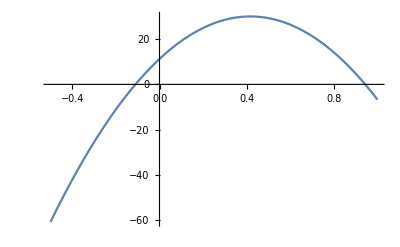

```mathematica
Plot[smallDiscr/.{a->0.5, b->0.5, c->0, n->5},{x,-0.5,1}]
```

Unfortunately, this polynomial becomes negative for x < 1. Let’s see where it becomes negative by plugging in the second to last endpoint of the lower boundary.

```mathematica
Simplify[smallDiscr/.{x->e2[n/(n-1),0,n-1,n]}]
```

-((-9 a b^2-b^3+27 a^2 c) (-2+n)^2)/(-1+n)^2

```mathematica
Simplify[smallDiscr/.{x->0}]
```

-((-9 a b^2-b^3+27 a^2 c) (-2+n)^2)

```mathematica
Simplify[smallDiscr/.{x->e2[n/(n-2),0,n-2,n]}]
```

(18 a b^2 (-2+n)^3+2 b^3 (-2+n)^3+27 a^3 (-3+n) n^2-27 a^2 (c (-4+n)^2 (-1+n)-b (-3+n) n^2))/((-2+n)^2 (-1+n))

Here, it is positive, which means that as long as the discriminant is nonnegative on the last segment of the lower boundary, it is nonnegative on the entire domain. Let us plug in the equation for the last segment of the lower boundary.

```mathematica
Simplify[discr/.{x->e2[t,n-k*t,k,n],y->e3[t,n-k*t,k,n]}/.{k->n-1}]
```

-4 (-9 a b^2-b^3+27 a^2 c) (-1+t)^6

We see that in this region, it is also nonegative, as desired.